### data loading

```mathematica
p0s={3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{ 999999, 999999, 999999,999999, 999999,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 999999, 999999, 999999,999999, 999999,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{ 999999, 999999, 999999,999999, 999999,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{ 1, 1, 1,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
tauAlphaResults={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3},{1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4}};
```

```mathematica
testData=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.750/energy/timePotentialEnergy_N4096_p3.7500_T0.01000000_waitingTime40000_idx13.nc","Data"]
```

LibraryFunction::fpexc: Numeric data containing a floating point exception (NaN or Inf) encountered.

<|/firstValue→NumericArray[…],/secondValue→$Failed|>

```mathematica
Normal[testData[[2,;;10]]]
```

Part::take: Cannot take positions 1 through 10 in $Failed.

Part::take: Cannot take positions 1 through 10 in /secondValue→$Failed.

{/firstValue→NumericArray[…],/secondValue→$Failed}⟦2,1;;10⟧

```mathematica
potentialEnergy=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/energy/timePotentialEnergy_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.775/energy/timePotentialEnergy_N4096_p3.7750_T0.02500000_waitingTime10000_idx18.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.775/energy/timePotentialEnergy_N4096_p3.7750_T0.01600000_waitingTime10000_idx16.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p3.775/energy/timePotentialEnergy_N4096_p3.7750_T0.00560000_waitingTime70000_idx14.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
potentialEnergyMean=Table[Table[Mean[Flatten[Table[Normal[potentialEnergy[[p,T,i,2]]],{i,Length[potentialEnergy[[p,T]]]}]]],{T,Length[potentialEnergy[[p]]]}],{p,Length[p0s]}]
```

{{92.558,39.4048,25.333,13.4682,10.664,7.35262,6.05985,3.33024,1.8053,1.23463,0.953921,0.550404,0.36181,0.307366,0.217394,0.181774,0.145827},{152.345,97.2512,77.9009,40.8781,25.7052,20.6972,16.4732,13.2945,10.3933,8.5897,7.0806,5.80263,4.52099,3.17953,2.23183,1.71777},{162.004,103.642,83.3474,67.2335,43.2137,26.6228,21.0422,16.4214,12.9412,9.91355,7.91592,7.1419,6.38132,5.63544},{90.3578,73.2449,58.5141,46.2191,33.8444,27.3273,23.9429,20.6192,18.9366,17.2908,15.1989,13.233,12.6873},{189.85,122.857,99.3333,80.1086,63.8756,49.735,41.9562,33.4225,29.3493,25.4851,23.3311}}

```mathematica
potentialEnergySTD=Table[Table[StandardDeviation[Flatten[Table[Normal[potentialEnergy[[p,T,i,2]]],{i,Length[potentialEnergy[[p,T]]]}]]],{T,Length[potentialEnergy[[p]]]}],{p,Length[p0s]}]
```

{{1.9608,0.75171,0.496049,0.286278,0.194223,0.117487,0.0982405,0.0523535,0.028243,0.0180677,0.0131433,0.00805191,0.00586214,0.00471782,0.00312043,0.00277968,0.00215494},{3.1117,1.51863,1.60178,0.8606,0.537023,0.366975,0.312074,0.271247,0.192208,0.157243,0.123365,0.101727,0.0779738,0.0537262,0.0363527,0.0277151},{3.26804,2.32006,1.60093,1.24436,0.788015,0.511164,0.423118,0.360881,0.262238,0.176964,0.153551,0.137485,0.147202,0.0994712},{1.62908,1.62433,1.04361,0.926771,0.616631,0.531975,0.558894,0.419378,0.415723,0.348552,0.365608,0.249228,0.263271},{3.16266,1.88271,1.9413,1.43264,1.25905,0.939367,0.804806,0.733423,0.631299,0.560079,0.544372}}

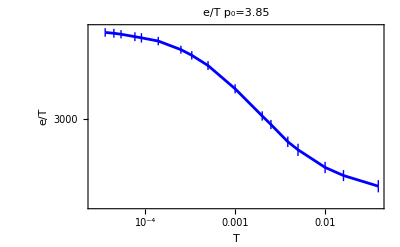
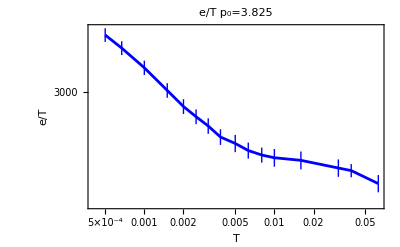
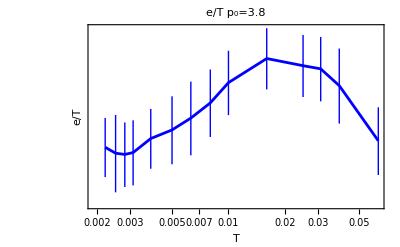
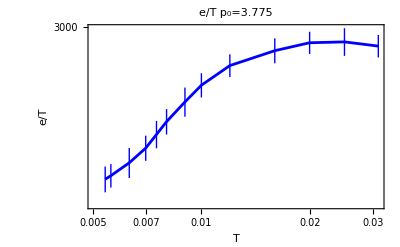
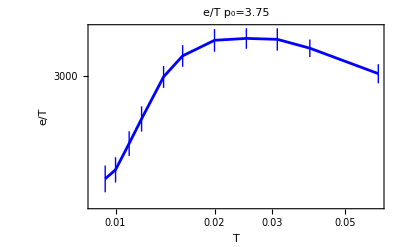

```mathematica
potentialScaledByTPlot=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Around[potentialEnergyMean[[p,T]],potentialEnergySTD[[p,T]]]/temperatures[[p,T]]},{T,1,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->Blue,Joined->True,FrameLabel->{"T","e/T"},PlotLabel->"e/T p_0="<>ToString[p0s[[p]]],ImageSize->400]],{p,1,Length[p0s]}]
```

```mathematica
tauEstimate[[1,-1]]
```

999999

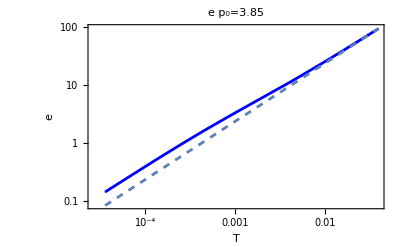
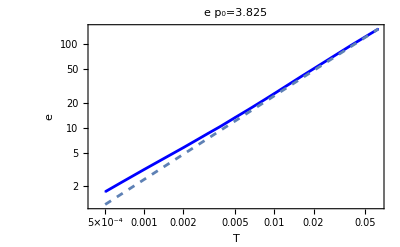
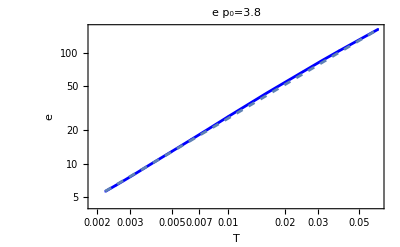
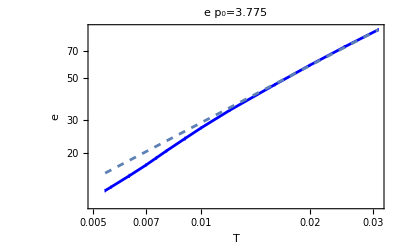
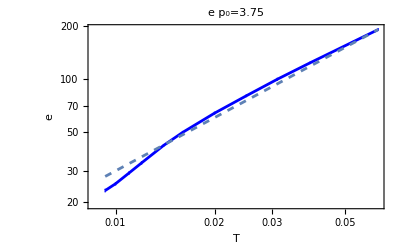

```mathematica
potentialPlot=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Around[potentialEnergyMean[[p,T]],potentialEnergySTD[[p,T]]]},{T,1,Length[temperatures[[p]]]}],PlotRange->All,PlotStyle->Blue,Joined->True,FrameLabel->{"T","e"},PlotLabel->"e p_0="<>ToString[p0s[[p]]],ImageSize->400],LogLogPlot[potentialEnergyMean[[p,1]]/temperatures[[p,1]]*x,{x,temperatures[[p,1]],temperatures[[p,-1]]},PlotStyle->Dashed]],{p,1,Length[p0s]}]
```

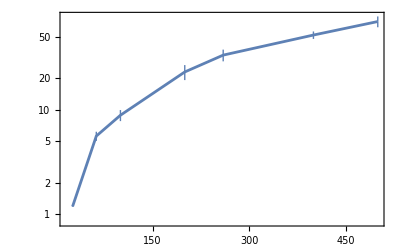
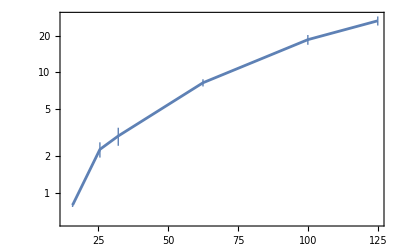
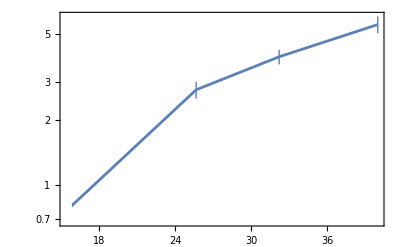

```mathematica
Table[Show[ListLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaResults[[p,T]]},{T,Length[temperatures[[p]]]-10}]},Joined->True,PlotRange->All,ImageSize->400],LogPlot[10000,{x,10,50000},PlotStyle->{Thin,Red}]],{p,3}]
```

```mathematica
Export["/home/chengling/Research/updates/0209025/potential2D.jpeg",Grid[Partition[Flatten[{potentialPlot,potentialScaledByTPlot}],5]],ImageResolution->200]
```

/home/chengling/Research/updates/0209025/potential2D.jpeg

```mathematica
Export["/home/chengling/Research/updates/0209025/potential2DVertical.jpeg",Grid[Partition[Flatten[Table[{potentialPlot[[s]],potentialScaledByTPlot[[s]]},{s,5}]],2]],ImageResolution->200]
```

/home/chengling/Research/updates/0209025/potential2DVertical.jpeg